```mathematica
Clear[ode,iconds,soln,odeOperator,xx];ode=ξ θ''[ξ]+2θ'[ξ]-ξ(Exp[-θ[ξ]]);iconds={θ[0]==0,θ'[0]==0};odeOperator=ξ D[#,{ξ,2}]+2D[#,ξ]-ξ Exp[-#]&;xx=Series[θ[ξ],{ξ,0,6}];soln=SolveAlways[Join[{odeOperator[xx]==0},iconds],ξ];Normal[xx/.soln[[1]]]
Normal[D[xx,ξ]/.soln[[1]]]
```

Solve::incnst: Inconsistent or redundant transcendental equation. After reduction, the bad equation is -Log[ⅇ^θ[0]] == 0.

SolveAlways::ifun: Inverse functions are being used by SolveAlways, so some solutions may not be found; use Reduce for complete solution information.

ξ^2/6-ξ^4/120+ξ^6/1890

ξ/3-ξ^3/30+ξ^5/315

```mathematica
Clear[solnum];solnum=With[{eps=1*^-19},NDSolve[Join[{odeOperator[θ[ξ]]==0},{θ[eps]==eps^2/6,θ'[eps]==eps/3}],θ,{ξ,eps,30000},WorkingPrecision->20]]
```

{{θ→InterpolatingFunction[…]}}

```mathematica
Clear[θapp];θapp[ξ_]=Log[1+ξ^2/2 (1-(2/3+0.59858*^-6 ξ^6)/((1+1*^-6 ξ^6) (1+ξ^2/15)^.25) Cos[Sqrt[7]/4 Log[1+ξ^2/23.162231]])];
```

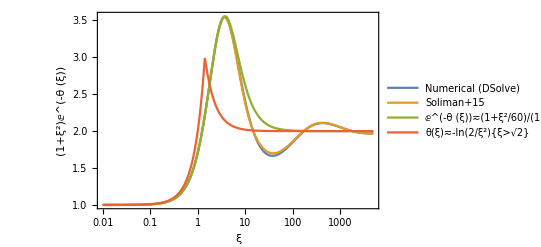

~/Desktop/le.png

```mathematica
LogLinearPlot[(1+ξ^2) {Exp[-θ[ξ]/.solnum[[1]]],Exp[-θapp[ξ]],(1+ξ^2/60)/(1+11 ξ^2/60+ξ^4/120),Piecewise[{{1,ξ<Sqrt[2]}},2/ξ^2]}//Evaluate,{ξ,0.01,5000},Frame->True,FrameLabel->{"ξ","(1+ξ^2)ⅇ^(-θ (ξ))"},PlotLegends->{"Numerical (DSolve)","Soliman+15","ⅇ^(-θ (ξ))≂(1+ξ^2/60)/(1+11ξ^2/60+ξ^4/120)","θ(ξ)≂-ln(2/ξ^2){ξ>√2}"},LabelStyle->{FontSize->12}]
Export["~/Desktop/le.png",%]
```

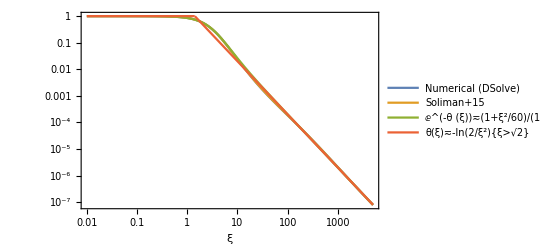

```mathematica
LogLogPlot[ {Exp[-θ[ξ]/.solnum[[1]]],Exp[-θapp[ξ]],(1+ξ^2/60)/(1+11 ξ^2/60+ξ^4/120),Piecewise[{{1,ξ<Sqrt[2]}},2/ξ^2]}//Evaluate,{ξ,0.01,5000},Frame->True,FrameLabel->{"ξ",""},PlotLegends->{"Numerical (DSolve)","Soliman+15","ⅇ^(-θ (ξ))≂(1+ξ^2/60)/(1+11ξ^2/60+ξ^4/120)","θ(ξ)≂-ln(2/ξ^2){ξ>√2}"},LabelStyle->{FontSize->12}]
```

```mathematica
FindMaximum[Exp[-θ[ξ]]ξ^4θ'[ξ]^2/.solnum,{ξ,5}]
FindMaximum[ξ θ'[ξ]/.solnum,{ξ,7}]
ξ θ'[ξ]/5/.solnum/.Out[-2][[2]]
```

{17.5635,{ξ→6.45075}}

{2.51755,{ξ→8.99311}}

{0.486901}

```mathematica
ξ^2 θ'[ξ]/.solnum[[1]]/.ξ->10^3//ScientificForm
```

2.04780028776547×10^3

```mathematica
Simplify[4π ρ0 l^3 ξ^2θ'[ξ]//.{ρ0->Pa/ζ^2Exp[θ[ξ]],l->√(ζ^2/(4π GG ρ0))},ζ>0 &&GG>0 &&Pa>0]
```

(√(ⅇ^(-θ[ξ])/Pa) ζ^4 ξ^2 θ'[ξ])/(2 GG^(3/2) √π)

```mathematica
Simplify[ξ^2θ'[ξ]/.θ->Function[x,-Log[2/x^2]],ξ>0]
```

2 ξ

```mathematica
Exp[-θ[ξ]/2]ξ^2θ'[ξ]/.θ->Function[x,-Log[2/x^2]]//Evaluate
```

2 √2 √(1/ξ^2) ξ

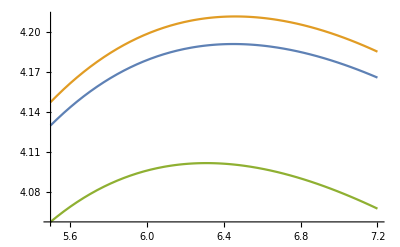

```mathematica
Plot[Exp[-θ[ξ]/2]ξ^2θ'[ξ]/.#&/@{solnum[[1]],θ->θapp,θ->Function[ξ,-Log[(1+ξ^2/60)/(1+11 ξ^2/60+ξ^4/120)]]}//Evaluate,{ξ,5.5,7.2}]
```

```mathematica
$MachinePrecision
```

15.9546

```mathematica
crit=FindMaximum[Exp[-θ[ξ]/2]ξ^2θ'[ξ]/.solnum[[1]],{ξ,6}]
crit[[1]]/Sqrt@(4π)
1/ξ/θ'[ξ]/.solnum[[1]]/.crit[[2]]
{ξ,Exp[θ[ξ]]}/.solnum[[1]]/.crit[[2]]
```

{4.19088,{ξ→6.45075}}

1.18223

0.410761

{6.45075,14.042}

```mathematica
Simplify[{ξ l}//.{l->(ζ^2/(4π GG ρ0))^(1/2),ρ0->ζ^6/(4π GG^3M^2)ξ^4(θ'[ξ])^2},θ'[ξ]>0&&ξ>0&&GG>0&&M>0&&ζ>0]
```

{(GG M)/(ζ^2 ξ θ'[ξ])}

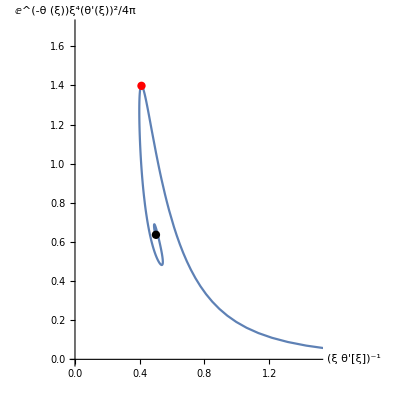

```mathematica
ParametricPlot[{1/(ξ θ'[ξ]),Exp[-θ[ξ]]ξ^4(θ'[ξ])^2/4/π}/.solnum[[1]],{ξ,.1,30000},AspectRatio->1,PlotRange->{{0,1.5},{0,1.7}},PlotPoints->5000,AxesLabel->{"(ξ θ'[ξ])^-1","ⅇ^(-θ (ξ))ξ^4(θ'(ξ))^2/4π"},LabelStyle->{FontSize->12},Epilog->{PointSize[0.015],Red,Point[{ 0.41076,17.5635/4/π}],Black,Point[{1/2,2/π}]}]
```

```mathematica
Export["~/public_html/Astronomy/pR.png",%]
```

~/public_html/Astronomy/pR.png

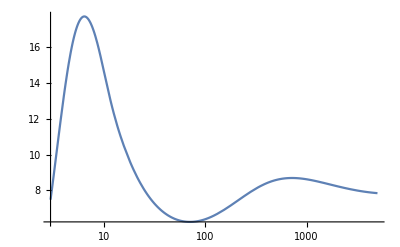

```mathematica
LogLinearPlot[{Exp[-θapp[ξ]]ξ^4(θapp'[ξ])^2},{ξ,3,5000},PlotRange->All]
```

```mathematica
Exp[-θ[ξ]]ξ^4(θ'[ξ])^2/.θ->Function[x,-Log[2/x^2]]
```

8

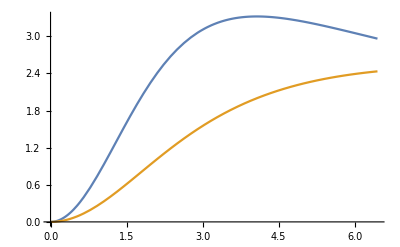

```mathematica
Plot[{ξ^2Exp[-θ[ξ]],ξ θ'[ξ]}/.solnum[[1]]//Evaluate,{ξ,0.,6.451},PlotRange->All]
```

```mathematica
Σc=ρ0*2*l*NIntegrate[Exp[-θ[x]],{x,0,ξ}];MM=4π l^3 ρ0 ξ^2θ'[ξ];Σm=MM/(π(l ξ)^2);ρm=MM/(4π/3*(l ξ)^3);
{Σc/Σm,Exp[θ[ξ]],ρ0/ρm}/.solnum[[1]]/.ξ->6.45075
```

{3.56003,14.042,5.69756}

```mathematica
FindRoot[(ξ^2Exp[-θ[ξ]]/.solnum[[1]])==(6.451^2Exp[-θ[6.451]]/.solnum[[1]]),{ξ,2}][[1,2]]
```

2.73772

```mathematica
FindMaximum[Exp[-θ[ξ]/2]ξ^2(θ'[ξ])/.solnum[[1]],{ξ,6.5}]
```

{4.19088,{ξ→6.45075}}

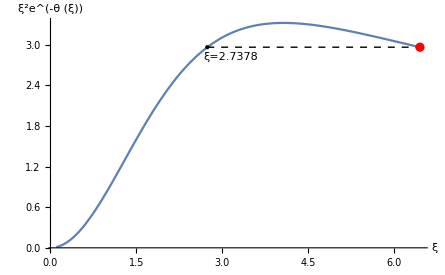

```mathematica
Block[{ξ2,aux},With[{ξmin=FindMaximum[Exp[-θ[ξ]/2]ξ^2θ'[ξ]/.solnum[[1]],{ξ,6.5},,AccuracyGoal->6][[2,1,2]]},ξ2=FindRoot[(ξ^2Exp[-θ[ξ]]/.solnum[[1]])==(ξmin^2Exp[-θ[ξmin]]/.solnum[[1]]),{ξ,2.7}][[1,2]];aux=ξmin^2Exp[-θ[ξmin]]/.solnum[[1]];Plot[ξ^2Exp[-θ[ξ]]/.solnum[[1]]//Evaluate,{ξ,0.1,ξmin},PlotRange->All,Epilog->{{PointSize[0.015],Red,Point[{6.451,aux}]},{Dashed,Line[{{ξ2,aux},{ξmin,aux}}]},Text["ξ="<>ToString@ξ2,{ξ2*1.15,aux*.95}],Point[{ξ2,aux}]},LabelStyle->{FontSize->12},AxesLabel->{Automatic,"ξ^2e^(-θ (ξ))"}]]]
```

```mathematica
Export["~/PRcons.png",%]
```

~/PRcons.png

```mathematica
FindMaximum[ξ θ'[ξ]/.solnum[[1]],{ξ,7}]
```

{2.51755,{ξ→8.99312}}

```mathematica
1/2.5175513114232886
```

0.397211

```mathematica
Maximize[x^3(1-x),x]
```

{27/256,{x→3/4}}

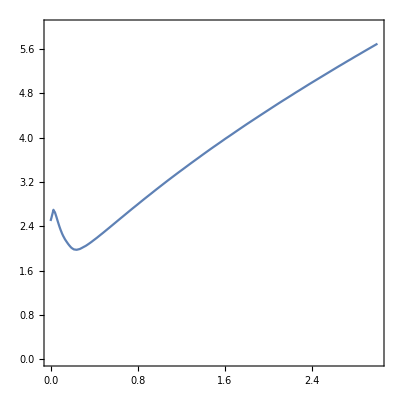

```mathematica
ContourPlot[l (R/l)^2(D[θapp[x],x]/.x->R/l)==5,{l,0,3},{R,0,6}]
```

```mathematica
Clear[MM,PPa];MM[l_,R_]:=(ζ^2/G)  l(R/l)^2θ'[R/l];PPa[l_,R_]:=ζ^4/(4π G l^2)Exp[-θ[R/l]];
```

```mathematica
-D[MM[l,R],R]/D[MM[l,R],l]/.R->ξ l/.θ''[ξ]->Exp[-θ[ξ]]-2θ'[ξ]/ξ//Simplify
```

1/(ξ-ⅇ^θ[ξ] θ'[ξ])

```mathematica
D[PPa[l,R],R]+D[PPa[l,R],l]*1/(ξ-ⅇ^θ[ξ] θ'[ξ])//.{l-> R/ξ}//Simplify
%//TeXForm
```

(ⅇ^(-θ[ξ]) ζ^4 ξ^3 (-2+ⅇ^θ[ξ] θ'[ξ]^2))/(4 G π R^3 (ξ-ⅇ^θ[ξ] θ'[ξ]))

\frac{\zeta ^4 \xi ^3 e^{-\theta (\xi )} \left(e^{\theta (\xi )} \theta '(\xi )^2-2\right)}{4 \pi  G R^3 \left(\xi
   -e^{\theta (\xi )} \theta '(\xi )\right)}

```mathematica
(D[PPa[l,R],R]+D[PPa[l,R],l]*1/(ξ-ⅇ^θ[ξ] θ'[ξ])/.{l-> R/ξ}//Simplify)
%/.{Exp[-θ[ξ]]->1/(ζ^4/(4π G l^2 Pa)),Exp[θ[ξ]]->ζ^4/(4π G l^2 Pa),θ'[ξ]->G M/ζ^2/l/ξ^2}
%/.{l-> R/ξ}//Simplify
```

(ⅇ^(-θ[ξ]) ζ^4 ξ^3 (-2+ⅇ^θ[ξ] θ'[ξ]^2))/(4 G π R^3 (ξ-ⅇ^θ[ξ] θ'[ξ]))

(l^2 Pa (-2+(G M^2)/(4 l^4 Pa π ξ^4)) ξ^3)/(R^3 (-(M ζ^2)/(4 l^3 Pa π ξ^2)+ξ))

(Pa (G M^2-8 Pa π R^4))/(4 Pa π R^5-M R^2 ζ^2)

```mathematica
Simplify[D[PPa[l,R],R]+D[PPa[l,R],l]*1/(ξ-ⅇ^θ[ξ] θ'[ξ])//.{l-> R/ξ,Exp[-θ[ξ]]->1/(ζ^4/(4π G l^2 Pa)),Exp[θ[ξ]]->ζ^4/(4π G l^2 Pa),θ'[ξ]->G M/ζ^2/l/ξ^2},MM>0 &&l>0 &&PPa>0&&ξ>0&&R>0&&ζ>0&&G>0&&V>0&&NN>0 &&m>0]
```

(Pa (G M^2-8 Pa π R^4))/(4 Pa π R^5-M R^2 ζ^2)

```mathematica
Simplify[1/(4π R^2)(Pa (G M^2-8 Pa π R^4))/(4 Pa π R^5-M R^2 ζ^2)/(-2/3*Pa/V)/.{R->(3 V/4/π)^(1/3)}]
```

((6 π)^(1/3) V^(1/3) (-G M^2 π^(1/3)+3 6^(1/3) Pa V^(4/3)))/(3 Pa V-M ζ^2)

```mathematica
Numerator[-((6^(2/3) G M^2 π^(1/3))/V^(1/3)-18 Pa V)/(18 Pa V-6 M ζ^2)]
```

```mathematica
-(6^(2/3) G M^2 π^(1/3))/(V^(1/3)18 Pa V)/((4π/3)^(1/3)/6)
```

-(G M^2)/(Pa V^(4/3))

```mathematica
Simplify[(Pa (G M^2*0-8 Pa π R^4))/(4 Pa π R^5-M R^2 ζ^2)/.ζ^2->Pa*4π/3R^3/M]
```

-(3 Pa)/R

```mathematica
3θ'[ξ]Exp[θ[ξ]]/ξ/.θ->θapp/.ξ->6.450750599629285
```

2.46367

```mathematica
Simplify[{Pa/V,MM ζ^2/Pa/V,G MM^2/Pa/V^(4/3)}/.{V->x(G MM/ζ^2)^3,Pa->p ζ^8/G^3/MM^2},MM>0 &&l>0 &&PPa>0&&ξ>0&&R>0&&ζ>0&&G>0&&V>0&&NN>0 &&m>0]
```

{(p ζ^14)/(G^6 MM^5 x),1/(p x),1/(p x^(4/3))}

```mathematica
{4π/3/ξ^3/θ'[ξ]^3,Exp[-θ[ξ]]ξ^4θ'[ξ]^2/4/π}/.solnum[[1]]/.ξ->5
```

{0.37276336697612024,1.29249581030668081}

{0.37276336697612024,1.29249581030668081}

{{p→InterpolatingFunction[…]}}

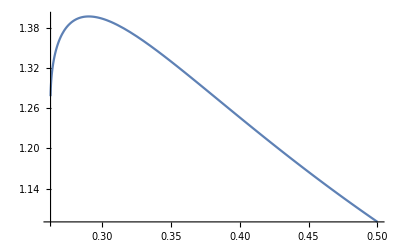

```mathematica
{4π/3/ξ^3/θ'[ξ]^3,Exp[-θ[ξ]]ξ^4θ'[ξ]^2/4/π}/.solnum[[1]]/.ξ->5
ssPV=NDSolve[{p'[x]==-2/3*p[x]/x*(1-(4π/3)^(1/3)/(6 p[x] x^(4/3)))/(1-(3p[x] x)^(-1)),p[%[[1]]]==%[[2]]},p,{x,0.26255,1.5}]
Plot[p[x]/.ssPV[[1]],{x,0.26255,0.5}]
```

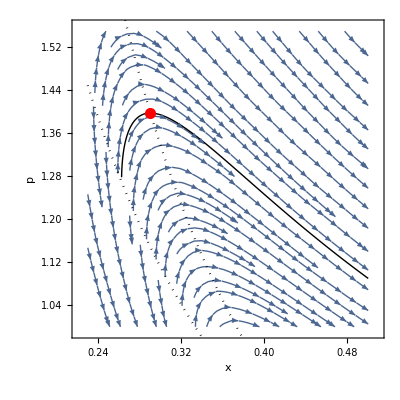

```mathematica
Show[StreamPlot[{1,-2/3*p/x*(1-(4π/3)^(1/3)/(6 p x^(4/3)))/(1-(3p x)^(-1))},{x,0.23,0.5},{p,1,1.55},Epilog->{PointSize[0.02],Red,Point[{(4π/3)0.41076^3,17.5635/4/π}]},FrameLabel->{"x","p"},LabelStyle->{FontSize->12}],Plot[{p[x]/.ssPV[[1]],(4π/3)^(1/3)/(6 x^(4/3))},{x,0.26255,.5},PlotStyle->{{Black,Thick},{Black,Dotted}}],Plot[1/3/x,{x,0.23,.5},PlotStyle->{Black,Dotted}]]
```

```mathematica
Export["~/public_html/Astronomy/px.png",%];
```

```mathematica
{(4π/3)0.41076^3,17.5635/4/π}
```

{0.290304,1.39766}